Note: requires the gapnew.dat file to be in the same folder.

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Libraries\_Git public\Wolfram-Mathematica

```mathematica
Needs["NumericalCalculus`"];
```

### Constants in SI units

```mathematica
γ= 10^-4;(*Dynes paramter in units of Δ0 which is normalized to 1*)
kB=1.3806504*10^-23; 
q = 1.602176487*10^-19;
Φ0=2 10^-15;
ℏ=1.054571628251774*10^-34;
```

### Parameters (Values of Aluminum)

```mathematica
vF= 2.3 10^6; (*Fermi velocity*)
Δ0= 212.5 1.6 10^-25; (*the gap of Aluminium*)
Tc = Δ0/(1.764*kB); (*BCS critical temperature*)
ξ0=ℏ*vF; (*The Fermi velocity cancels out of the equations, because L is inputted in units of ξ0 and is only relevant from the fabrication poin of view*)
ϕ0=0;(* Phase difference in the middle of the junction, set zo zero for the moment*)

R = 1.0 10^4; (*Tunnel junction resistance*)
delta=Interpolation[Import[NotebookDirectory[]<>"\\gapnew.dat","Table"]]; (*Import a measurement of the superconducting gap*)

Print["For Fermi velocity vF = ",vF," m/s the real (not rescaled) value of ξ0 is ",ξ0/Δ0," m"]
Print["For a Fermi velocity vF = ",760," m/s the real (not rescaled) value of ξ0 is ",ℏ*760/Δ0," m"]
Print["Tc is ",Tc," K"]
```

For Fermi velocity vF = 2.3×10^6 m/s the real (not rescaled) value of ξ0 is 7.13387×10^-6 m

For a Fermi velocity vF = 760 m/s the real (not rescaled) value of ξ0 is 2.35728×10^-9 m

Tc is 1.39604 K

### TSQUIPT functions

Φn is Φ/Φ0; the flux through the junction, normalized by the quantum of flux
Δ is normalized by Δ0 and T by Tc

```mathematica
Δ[T_]:=delta[T];
ξ[T_]:=ℏ*vF/(Δ[T]);
fermi[energy_,temperature_]:= 1/(Exp[(1.764 energy)/temperature]+1);

ρBCS[energy_,T_]:=Abs[Re[(energy+ ⅈ γ)/(√((energy+ⅈ γ)^2-Δ[T]^2))  ]];
ps[Φn_,L_]:=(Pi*ℏ)/L*Φn; (*Finite Cooper pair momentum, simplified*)
energyMin[energy_,Φn_,L_]:=energy-vF*ps[Φn,L]/2;
energyPlus[energy_,Φn_,L_]:=energy+vF*ps[Φn,L]/2;

(* Δ[T]*ξ[T] in the cosine replaced with ℏ vF -> there is no T dependence in the cosine. This DoS does not include the ABS *)
ρ[energy_,Φn_,T_,L_]:=Abs[energyMin[energy,Φn,L]]/(√(energyMin[energy,Φn,L]^2-Δ[T]^2)) HeavisideTheta[Abs[energyMin[energy,Φn,L]
]-Δ[T]]*((energyMin[energy,Φn,L]^2-Δ[T]^2)/(energyMin[energy,Φn,L]^2-Δ[T]^2 Cos[(ϕ0+Pi*Φn)/2-(energyMin[energy,Φn,L]*L)/(ℏ vF)]^2))+Abs[energyPlus[energy,Φn,L]]/(√(energyPlus[energy,Φn,L]^2-Δ[T]^2)) HeavisideTheta[Abs[energyPlus[energy,Φn,L]
]-Δ[T]]*((energyPlus[energy,Φn,L]^2-Δ[T]^2)/(energyPlus[energy,Φn,L]^2-Δ[T]^2 Cos[(ϕ0+Pi*Φn)/2+(energyPlus[energy,Φn,L]*L)/(ℏ vF)]^2));

η=0.01; 

ρABS[energy_,Φn_,T_,L_]:=Re[4 ⅇ^(ⅈ (ϕ0+Pi*Φn)) (((ⅇ^((2 ⅈ L Re[energyMin[energy + ⅈ η,Φn,L]])/(ℏ vF)) (-Δ[T]^2+energyMin[energy + ⅈ η,Φn,L]^2))/((ⅇ^((2 ⅈ L energyMin[energy + ⅈ η,Φn,L])/(ℏ vF)) (-1+√(1-Δ[T]^2/energyMin[energy + ⅈ η,Φn,L]^2))+ⅇ^(ⅈ (ϕ0+Pi*Φn)) (1+√(1-Δ[T]^2/energyMin[energy + ⅈ η,Φn,L]^2))) energyMin[energy + ⅈ η,Φn,L]^2 (ⅇ^(ⅈ (ϕ0+Pi*Φn)) (-1+Conjugate[√(1-Δ[T]^2/energyMin[energy + ⅈ η,Φn,L]^2)])+ⅇ^((2 ⅈ L Conjugate[energyMin[energy + ⅈ η,Φn,L]])/(ℏ vF)) (1+Conjugate[√(1-Δ[T]^2/energyMin[energy + ⅈ η,Φn,L]^2)]))))(Abs[energyMin[energy + ⅈ η,Φn,L]]/Sqrt[energyMin[energy + ⅈ η,Φn,L]^2-Δ[T]^2])+((ⅇ^((2 ⅈ L Re[energyPlus[energy + ⅈ η,Φn,L]])/(ℏ vF)) (-Δ[T]^2+energyPlus[energy + ⅈ η,Φn,L]^2))/((1+ⅇ^(ⅈ ((ϕ0+Pi*Φn)+(2 L energyPlus[energy + ⅈ η,Φn,L])/(ℏ vF))) (-1+√(1-Δ[T]^2/energyPlus[energy + ⅈ η,Φn,L]^2))+√(1-Δ[T]^2/energyPlus[energy + ⅈ η,Φn,L]^2)) energyPlus[energy + ⅈ η,Φn,L]^2 (-1+ⅇ^(ⅈ ((ϕ0+Pi*Φn)+(2 L Conjugate[energyPlus[energy + ⅈ η,Φn,L]])/(ℏ vF)))+(1+ⅇ^(ⅈ ((ϕ0+Pi*Φn)+(2 L Conjugate[energyPlus[energy + ⅈ η,Φn,L]])/(ℏ vF)))) Conjugate[√(1-Δ[T]^2/energyPlus[energy + ⅈ η,Φn,L]^2)])))(Abs[energyPlus[energy + ⅈ η,Φn,L]]/Sqrt[energyPlus[energy + ⅈ η,Φn,L]^2-Δ[T]^2]))];
ρABSMin[energy_,Φn_,T_,L_]:=Re[4 ⅇ^(ⅈ (ϕ0+Pi*Φn)) (((ⅇ^((2 ⅈ L Re[energyMin[energy + ⅈ η,Φn,L]])/(ℏ vF)) (-Δ[T]^2+energyMin[energy + ⅈ η,Φn,L]^2))/((ⅇ^((2 ⅈ L energyMin[energy + ⅈ η,Φn,L])/(ℏ vF)) (-1+√(1-Δ[T]^2/energyMin[energy + ⅈ η,Φn,L]^2))+ⅇ^(ⅈ (ϕ0+Pi*Φn)) (1+√(1-Δ[T]^2/energyMin[energy + ⅈ η,Φn,L]^2))) energyMin[energy + ⅈ η,Φn,L]^2 (ⅇ^(ⅈ (ϕ0+Pi*Φn)) (-1+Conjugate[√(1-Δ[T]^2/energyMin[energy + ⅈ η,Φn,L]^2)])+ⅇ^((2 ⅈ L Conjugate[energyMin[energy + ⅈ η,Φn,L]])/(ℏ vF)) (1+Conjugate[√(1-Δ[T]^2/energyMin[energy + ⅈ η,Φn,L]^2)]))))(Abs[energyMin[energy + ⅈ η,Φn,L]]/Sqrt[energyMin[energy + ⅈ η,Φn,L]^2-Δ[T]^2]))];

transmission[energy_,Φn_,T_,L_]:= HeavisideTheta[Abs[energyMin[energy,Φn,L]
]-Δ[T]]*((energyMin[energy,Φn,L]^2-Δ[T]^2)/(energyMin[energy,Φn,L]^2-Δ[T]^2 Cos[(ϕ0+Pi*Φn)/2-(energyMin[energy,Φn,L]*L)/(ℏ vF)]^2))+ HeavisideTheta[Abs[energyPlus[energy,Φn,L]
]-Δ[T]]*((energyPlus[energy,Φn,L]^2-Δ[T]^2)/(energyPlus[energy,Φn,L]^2-Δ[T]^2 Cos[(ϕ0+Pi*Φn)/2+(energyPlus[energy,Φn,L]*L)/(ℏ vF)]^2));
(*There are singularities in ρ when: energy = Δ(1-(π ξ0)/(2L)Φ/Φ0), energy = Δ(1+(π ξ0)/(2L)Φ/Φ0) *)
(*singularities are avoided*)
(*AccuracyGoal can be used to reduce the amount of work done if the function is zero*)
chargeCurrentABS[Φn_,tempN_,tempS_,V_?NumericQ,L_,intRange_]:= (*Δ0/(q R)*)Re[NIntegrate[ρABS[energy,Φn,tempS,L]*(fermi[energy-V,tempN]-fermi[energy,tempS]),{energy,-intRange,-(Δ[tempS]+vF*ps[Φn,L]/2),-(Δ[tempS]-vF*ps[Φn,L]/2),(Δ[tempS]-vF*ps[Φn,L]/2),(Δ[tempS]+vF*ps[Φn,L]/2),intRange}, MaxRecursion->25,MinRecursion->3,AccuracyGoal->4, Method->{"Oscillatory","SymbolicProcessing"->False}]];

(*Finds the V corresponding to a given Bias current*)
root[flux_,bias_,temp_,L_] :=(*findV/.*){findV}/.FindRoot[chargeCurrentABS[flux,temp,temp,findV,L ξ0,10]==bias,{findV,1.0}];
rootABS[flux_,bias_,temp_,L_] :=(*findV/.*){findV}/.FindRoot[chargeCurrentABS[flux,temp,temp,findV,L ξ0,10]==bias,{findV,1.0}];

rootopt[flux_,bias_,temp_,L_,Vstart_] :=(*findV/.*){findV}/.FindRoot[chargeCurrentABS[flux,temp,temp,findV,L ξ0,10]==bias,{findV,Vstart}];
rootoptABS[flux_,bias_,temp_,L_,Vstart_] :=(*findV/.*){findV}/.FindRoot[chargeCurrentABS[flux,temp,temp,findV,L ξ0,10]==bias,{findV,Vstart},MaxIterations->1000];
```

### SProbe functions (add BSC singularities like in SIN)

```mathematica
(*Charge Current for a tunnel coupled superconducting proble*)
chargeCurrentSProbe[Φn_,tempSProbe_,tempS_,V_,L_,intRange_]:= (*Δ0/(q R)*)NIntegrate[ρBCS[energy-V,tempSProbe]* ρ[energy,Φn,tempS,L]*(fermi[energy-V,tempSProbe]-fermi[energy,tempS]),{energy,-intRange,-(Δ[tempS]+vF*ps[Φn,Δ[tempS],L]/2),-(Δ[tempS]-vF*ps[Φn,Δ[tempS],L]/2),(Δ[tempS]-vF*ps[Φn,Δ[tempS],L]/2),(Δ[tempS]+vF*ps[Φn,Δ[tempS],L]/2),intRange}, MaxRecursion->25,MinRecursion->3,Method->{"Oscillatory","SymbolicProcessing"->False}];
```

```mathematica
(*Finds the V corrosponding with a given Bias current for a superconducting probe*)
rootSProbe[flux_,bias_,temp_,L_] :={findV}/.FindRoot[chargeCurrentSProbe[flux,temp,temp,findV,L ξ0,10]==bias,{findV,0}];
```

### SIN functions

```mathematica
(*Charge Current for a tunnel coupled superconducting proble*)
chargeCurrentSIN[tempSProbe_,tempS_,V_,intRange_]:= (*Δ0/(q R)*)NIntegrate[ρBCS[energy-V,tempSProbe]*(fermi[energy-V,tempSProbe]-fermi[energy,tempS]),{energy,-intRange,-Δ[tempS],Δ[tempS],intRange}, MaxRecursion->25,MinRecursion->3,Method->{"Oscillatory","SymbolicProcessing"->False}];
```

### SIS functions

```mathematica
(*Charge Current for a tunnel coupled superconducting proble*)
chargeCurrentSIS[tempSProbe_,tempS_,V_,intRange_]:= (*Δ0/(q R)*)NIntegrate[ρBCS[energy-V,tempSProbe]*ρBCS[energy,tempSProbe] *(fermi[energy-V,tempSProbe]-fermi[energy,tempS]),{energy,-intRange,-2Δ[tempS],2Δ[tempS],intRange}, MaxRecursion->25,MinRecursion->3,Method->{"Oscillatory","SymbolicProcessing"->False}];
```

### SNS SQUIPT functions

```mathematica
(*Normalized to the DOS at the Fermi level in absence of the proximity effect*)
```

```mathematica
ρSQUIPT[energy_,ϕ_,T_] :=Re[energy^2/(energy^2-Δ[T]^2 Cos[ϕ/2]^2)];
```

## General checks

### Gap

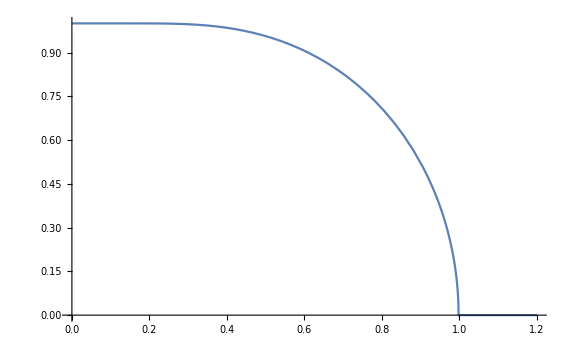

```mathematica
Plot[Δ[T],{T,0,1.2}]
```

### Temperature dependence of the coherence length

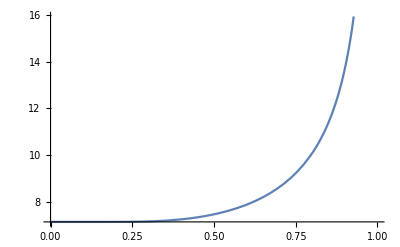

```mathematica
Plot[ξ[T]*10^6/Δ0,{T,0,1},PlotLegends->"ξ in μm as a function of T/Tc"]
```

### Modulation factor ρBSC compared to Heaviside thetha

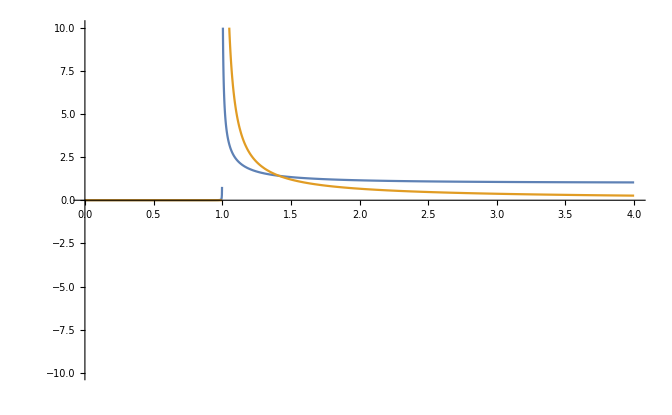

```mathematica
Plot[{ρBCS[energy,0.1],HeavisideTheta[energy-Δ[0.1]]* energy/(energy^2-Δ[0.1]^2)},{energy,0,4},PlotRange->10]
```

### Fermi function

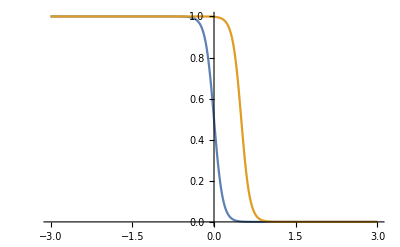

```mathematica
Module[{testV =  0.5/q,testT = 0.1Tc,testFlux = 0.5},
Plot[{fermi[energy,testT],fermi[energy-testV q,testT]},{energy,-3,3 }]
]
```

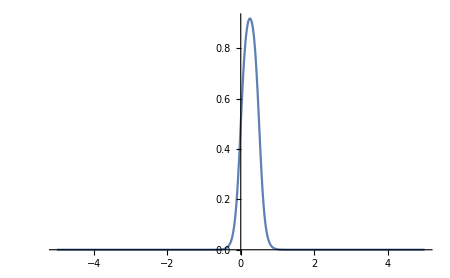

```mathematica
Module[{testV =  0.5/q,testT = 0.1Tc,testFlux = 0.5},
Plot[fermi[energy-testV q,testT]-fermi[energy,testT],{energy,-5,5 },PlotRange->Full]
]
```

## Plots DoS

```mathematica
Manipulate[Plot[ρABS[energy,0.5,0.1,L ξ0],{energy,-4,4}],{L,1,10}]
```

#### Length dependence

```mathematica
Module[{L = 1},
Print["Junction L =",L];
DensityPlot[Abs[ρABS[energy,flux,0.1,L ξ0]],{flux,-4,4},{energy,-2,2},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotRange->5,PlotPoints->100,PlotLegends->Automatic]
]
```

Junction L =1

-Graphics-

#### Temperature dependence

```mathematica
Module[{T = 0.5},
Print["Temperature (in units of T_C =",T];
DensityPlot[Abs[ρABS[energy,flux,T,ξ0]],{flux,-4,4},{energy,-2,2},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotRange->5,PlotPoints->200,PlotLegends->Automatic]
]
```

Temperature (in units of T_C =0.5

-Graphics-

#### ϕ0 dependence

```mathematica
Module[{ϕ0 = 0},
Print["Superconducting phase difference ϕ0 =",ϕ0];
DensityPlot[ρABS[energy,Φn,0.1,2ξ0],{Φn,-4,4},{energy,-2,2},ColorFunction->"BlueGreenYellow",Exclusions->None,PlotPoints->100,PlotLegends->Automatic]
]
```

Superconducting phase difference ϕ0 =0

-Graphics-

#### Cuts of ρ for various values of Φ

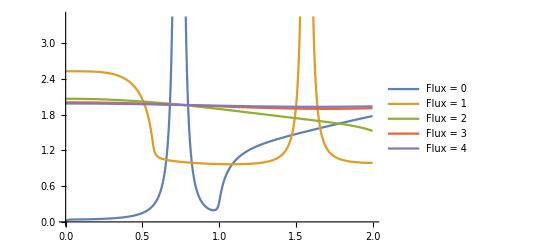

```mathematica
Module[{Length =  ξ0},
Plot[{Re[ρABS[energy,0,0.1,Length]],Re[ρABS[energy,1,0.1,Length]],Re[ρABS[energy,2,0.1,Length]],Re[ρABS[energy,3,0.1,Length]],Re[ρABS[energy,4,0.1,Length]]},{energy, 0,2},PlotLegends->{"Flux = 0","Flux = 1","Flux = 2","Flux = 3","Flux = 4"},PlotRange -> Automatic]]
```

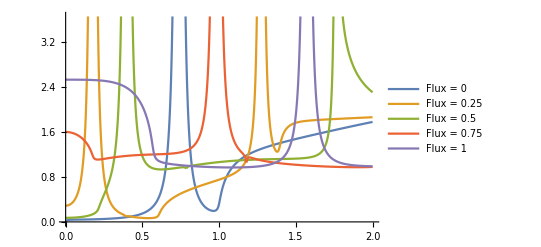

```mathematica
Module[{Length =  ξ0},
Plot[{Re[ρABS[energy,0,0.1,Length]],Re[ρABS[energy,0.25,0.1,Length]],Re[ρABS[energy,.5,0.1,Length]],Re[ρABS[energy,.75,0.1,Length]],Re[ρABS[energy,1,0.1,Length]]},{energy, 0,2},PlotLegends->{"Flux = 0","Flux = 0.25","Flux = 0.5","Flux = 0.75","Flux = 1"},PlotRange -> Automatic]]
```

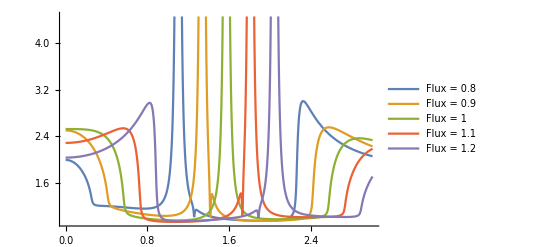

```mathematica
Module[{Length =  ξ0},
Plot[{Re[ρABS[energy,0.8,0.1,Length]],Re[ρABS[energy,0.9,0.1,Length]],Re[ρABS[energy,1,0.1,Length]],Re[ρABS[energy,1.1,0.1,Length]],Re[ρABS[energy,1.2,0.1,Length]]},{energy, 0,3},PlotLegends->{"Flux = 0.8","Flux = 0.9","Flux = 1","Flux = 1.1","Flux = 1.2"},PlotRange -> Automatic]]
```

## Plots IV

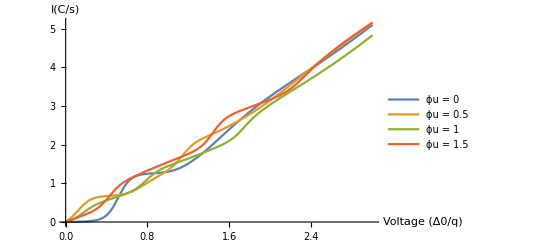

```mathematica
Plot[{
chargeCurrentABS[0,0.1,0.1,V,2ξ0,10],
chargeCurrentABS[0.5,0.1,0.1,V,2ξ0,10],
chargeCurrentABS[1,0.1,0.1,V,2ξ0,10],
chargeCurrentABS[1.5,0.1,0.1,V,2ξ0,10]},
{V,0,3},PlotRange->Full,PlotLegends->{"ϕu = 0","ϕu = 0.5","ϕu = 1","ϕu = 1.5"},PlotPoints-> Automatic,AxesLabel -> {"Voltage (Δ0/q)","I(C/s)"}]
```

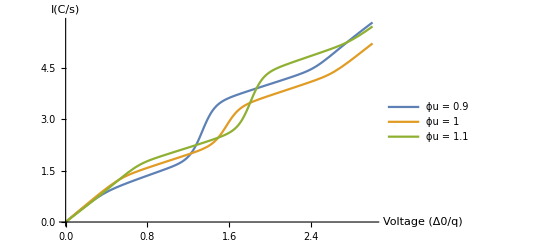

```mathematica
Plot[{
chargeCurrentABS[0.9,0.1,0.1,V,ξ0,10],
chargeCurrentABS[1,0.1,0.1,V,ξ0,10],
chargeCurrentABS[1.1,0.1,0.1,V,ξ0,10]},
{V,0,3},PlotRange->Full,PlotLegends->{"ϕu = 0.9","ϕu = 1","ϕu = 1.1"},PlotPoints-> Automatic,AxesLabel -> {"Voltage (Δ0/q)","I(C/s)"}]
```

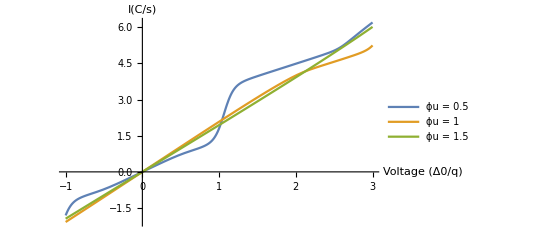

```mathematica
Plot[{
chargeCurrentABS[0.5,0.1,0.1,V,0.5ξ0,10],
chargeCurrentABS[1,0.1,0.1,V,0.5ξ0,10],
chargeCurrentABS[1.5,0.1,0.1,V,0.5ξ0,10]},
{V,-1,3},PlotRange->Full,PlotLegends->{"ϕu = 0.5","ϕu = 1","ϕu = 1.5"},PlotPoints-> Automatic,AxesLabel -> {"Voltage (Δ0/q)","I(C/s)"}]
```

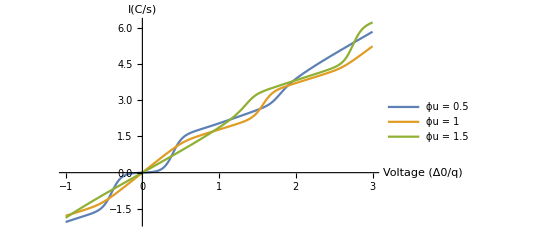

```mathematica
Plot[{
chargeCurrentABS[0.5,0.1,0.1,V,ξ0,10],
chargeCurrentABS[1,0.1,0.1,V,ξ0,10],
chargeCurrentABS[1.5,0.1,0.1,V,ξ0,10]},
{V,-1,3},PlotRange->Full,PlotLegends->{"ϕu = 0.5","ϕu = 1","ϕu = 1.5"},PlotPoints-> Automatic,AxesLabel -> {"Voltage (Δ0/q)","I(C/s)"}]
```

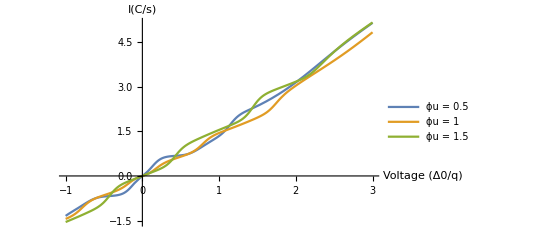

```mathematica
Plot[{
chargeCurrentABS[0.5,0.1,0.1,V,2ξ0,10],
chargeCurrentABS[1,0.1,0.1,V,2ξ0,10],
chargeCurrentABS[1.5,0.1,0.1,V,2ξ0,10]},
{V,-1,3},PlotRange->Full,PlotLegends->{"ϕu = 0.5","ϕu = 1","ϕu = 1.5"},PlotPoints-> Automatic,AxesLabel -> {"Voltage (Δ0/q)","I(C/s)"}]
```

### IV at T = 0.5 and T = 0.9

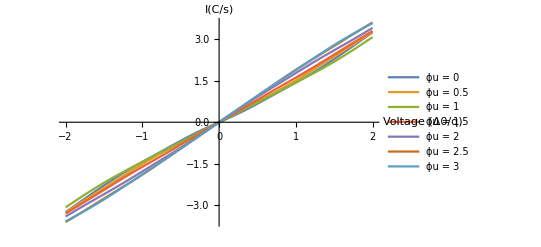

```mathematica
Plot[{
chargeCurrentABS[0,0.5,0.5,V,2ξ0,10],
chargeCurrentABS[0.5,0.5,0.5,V,2ξ0,10],
chargeCurrentABS[1,0.5,0.5,V,2ξ0,10],
chargeCurrentABS[1.5,0.5,0.5,V,2ξ0,10],
chargeCurrentABS[2,0.5,0.5,V,2ξ0,10],
chargeCurrentABS[2.5,0.5,0.5,V,2ξ0,10],
chargeCurrentABS[3,0.5,0.5,V,2ξ0,10]},
{V,-2,2},PlotRange->Full,PlotLegends->{"ϕu = 0","ϕu = 0.5","ϕu = 1","ϕu = 1.5","ϕu = 2","ϕu = 2.5","ϕu = 3"},PlotPoints-> Automatic,AxesLabel -> {"Voltage (Δ0/q)","I(C/s)"}]
```

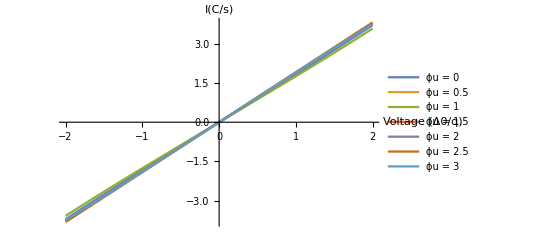

```mathematica
Plot[{
chargeCurrentABS[0,0.9,0.9,V,2ξ0,10],
chargeCurrentABS[0.5,0.9,0.9,V,2ξ0,10],
chargeCurrentABS[1,0.9,0.9,V,2ξ0,10],
chargeCurrentABS[1.5,0.9,0.9,V,2ξ0,10],
chargeCurrentABS[2,0.9,0.9,V,2ξ0,10],
chargeCurrentABS[2.5,0.9,0.9,V,2ξ0,10],
chargeCurrentABS[3,0.9,0.9,V,2ξ0,10]},
{V,-2,2},PlotRange->Full,PlotLegends->{"ϕu = 0","ϕu = 0.5","ϕu = 1","ϕu = 1.5","ϕu = 2","ϕu = 2.5","ϕu = 3"},PlotPoints-> Automatic,AxesLabel -> {"Voltage (Δ0/q)","I(C/s)"}]
```

## Plots VFlux at constant Ibias and its transfer function

#### Plots

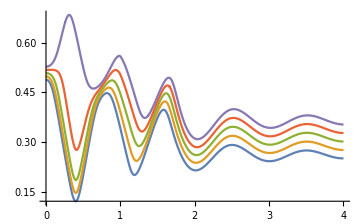
{573.895,-Graphics-}

```mathematica
Plot[{rootABS[flux,0.5,0.1,2][[1]],rootABS[flux,0.55,0.1,2][[1]],rootABS[flux,0.6,0.1,2][[1]],rootABS[flux,0.65,0.1,2][[1]],rootABS[flux,0.7,0.1,2][[1]]},{flux,0,4.0}]//AbsoluteTiming
```

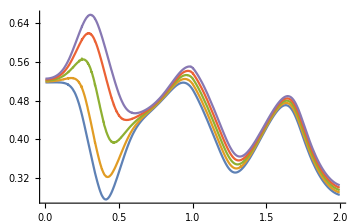
{645.556,-Graphics-}

```mathematica
Plot[{rootABS[flux,0.65,0.1,2][[1]],rootABS[flux,0.66,0.1,2][[1]],rootABS[flux,0.67,0.1,2][[1]],rootABS[flux,0.68,0.1,2][[1]],rootABS[flux,0.69,0.1,2][[1]]},{flux,0,2.0}]//AbsoluteTiming
```

π/2

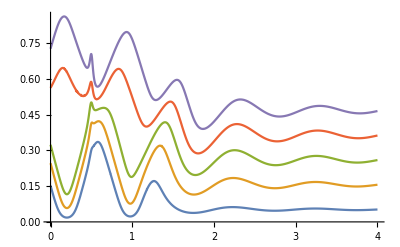

```mathematica
ϕ0=Pi/2
Plot[{rootABS[flux,0.1,0.1,2][[1]],rootABS[flux,0.3,0.1,2][[1]],rootABS[flux,0.5,0.1,2][[1]],rootABS[flux,0.7,0.1,2][[1]],rootABS[flux,0.9,0.1,2][[1]]},{flux,0,4.0}]
```

## Plots IFlux at constant bias, symmetrical and long

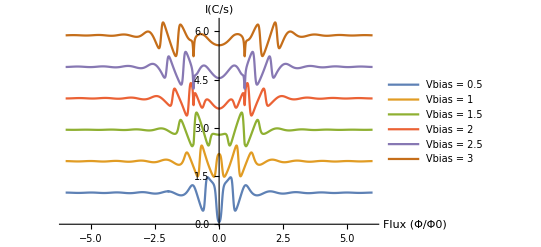

```mathematica
Plot[{
chargeCurrentABS[flux,0.1,0.1,0.5,1ξ0,10],
chargeCurrentABS[flux,0.1,0.1,1.0,1ξ0,10],
chargeCurrentABS[flux,0.1,0.1,1.5,1ξ0,10],
chargeCurrentABS[flux,0.1,0.1,2,1ξ0,10],
chargeCurrentABS[flux,0.1,0.1,2.5,1ξ0,10],
chargeCurrentABS[flux,0.1,0.1,3,1ξ0,10]},
{flux,-6,6},PlotRange->Full,PlotLegends->{"Vbias = 0.5","Vbias = 1","Vbias = 1.5","Vbias = 2","Vbias = 2.5","Vbias = 3"},PlotPoints-> Automatic,AxesLabel -> {"Flux (Φ/Φ0)","I(C/s)"}]
```

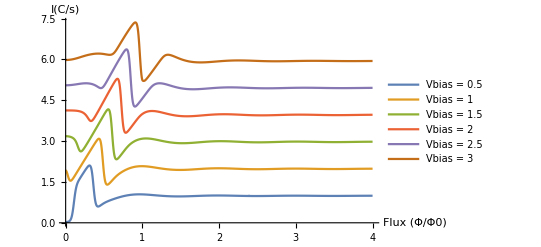

```mathematica
Plot[{
chargeCurrentABS[flux,0.1,0.1,0.5,0.5ξ0,10],
chargeCurrentABS[flux,0.1,0.1,1.0,0.5ξ0,10],
chargeCurrentABS[flux,0.1,0.1,1.5,.5ξ0,10],
chargeCurrentABS[flux,0.1,0.1,2,0.5ξ0,10],
chargeCurrentABS[flux,0.1,0.1,2.5,0.5ξ0,10],
chargeCurrentABS[flux,0.1,0.1,3,0.5ξ0,10]},
{flux,0,4},PlotRange->Full,PlotLegends->{"Vbias = 0.5","Vbias = 1","Vbias = 1.5","Vbias = 2","Vbias = 2.5","Vbias = 3"},PlotPoints-> Automatic,AxesLabel -> {"Flux (Φ/Φ0)","I(C/s)"}]
```

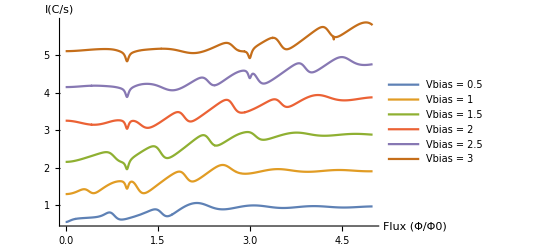

```mathematica
Plot[{
chargeCurrentABS[flux,0.1,0.1,0.5,2ξ0,10],
chargeCurrentABS[flux,0.1,0.1,1.0,2ξ0,10],
chargeCurrentABS[flux,0.1,0.1,1.5,2ξ0,10],
chargeCurrentABS[flux,0.1,0.1,2,2ξ0,10],
chargeCurrentABS[flux,0.1,0.1,2.5,2ξ0,10],
chargeCurrentABS[flux,0.1,0.1,3,2ξ0,10]},
{flux,0,5},PlotRange->Full,PlotLegends->{"Vbias = 0.5","Vbias = 1","Vbias = 1.5","Vbias = 2","Vbias = 2.5","Vbias = 3"},PlotPoints-> Automatic,AxesLabel -> {"Flux (Φ/Φ0)","I(C/s)"}]
```

## Plots Transfer function (dI(Φ))/dΦ

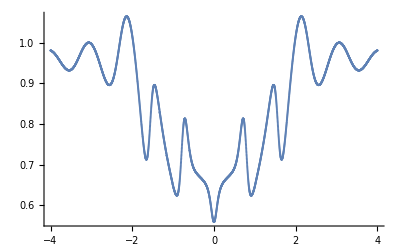

```mathematica
ListPlot[Table[{flux,Re[chargeCurrentABS[flux,0.1,0.1,0.5,2ξ0,10]]},{flux,-4,4,1/500}]]
```